# Mathematica as a Tool for Astronomy and Physics

## Lecture 6 Wintersemester 2009/10 Markus Röllig

## Graphic Fundamentals - continuation

### GraphicsComplex

Another possibility to represent 2-D or 3-D graphics is as a GraphicsComplex. GraphicsComplex[{pt_1,pt_2,…},data] represents a graphics complex in which coordinates given as integers i in graphics primitives in data are taken to be pt_i. GraphicsComplex provides a convenient way to build up meshes or simplicial complexes in which vertices of polygons are shared.

```mathematica
v={{1,0},{0,1},{-1,0},{0,-1}};
```

```mathematica
{Graphics[GraphicsComplex[v,Polygon[{1,2,3,4}]]],Graphics[GraphicsComplex[v,Line[{1,2,3,4,1}]]]}
```

The same in 3D

```mathematica
v={{0,0,0},{2,0,0},{2,2,0},{0,2,0},{1,1,2}};
```

```mathematica
i={{1,2,5},{2,3,5},{3,4,5},{4,1,5}};
```

```mathematica
{Graphics3D[{Opacity[.8],Yellow,GraphicsComplex[v,Polygon[i]]}],Graphics3D[{Thick,GraphicsComplex[v,Line[i]]}]}
```

A random selection of index coordinates:

```mathematica
p=Table[{Cos[2Pi/70 k],Sin[2Pi/70 k]},{k,70}];
```

```mathematica
Graphics[GraphicsComplex[p,Polygon[RandomSample[Range[70],70]]]]
```

Here are a few more example applications. Most surface and region plots produce GraphicsComplex:

```mathematica
pl=ParametricPlot[{r Cos[θ],r Sin[θ]},{r,1,2},{θ,0,2Pi/3},PlotRange->All]
```

You can use GraphicsComplex to transform the coordinates in this simple rotation:

```mathematica
pl/.GraphicsComplex[p_List,rest__]:>GraphicsComplex[RotationTransform[Pi/3][p],rest]
```

Point-extraction is also very simple :

```mathematica
pl/.GraphicsComplex[p_List,rest__]:>Point[p]
```

```mathematica
Show[pl,pl/.GraphicsComplex[p_List,rest__]:>Point[p]]
```

If ParametricPlot or ParametricPlot3D produces a curve the graphic structure is similar to regular plots:

```mathematica
pl1=ParametricPlot3D[{Sin[u],Cos[u],u/10},{u,0,1}]
```

```mathematica
InputForm[pl1]/.Line[__]:>Line["points"]
```

It is just a multi-point Line. But if surfaces are drawn, the parametric plot produces GraphicsComplex objects:

```mathematica
pl2=ParametricPlot3D[{Cos[u],Sin[u]+Cos[v],Sin[v]},{u,0,2π},{v,-π,π}];
```

```mathematica
InputForm[pl2]/.{Line[__]:>"Line",Rule[VertexNormals,__]_:>Rule[VertexNormals,"V-Normals"],Polygon[__]:>"Polygon",List[{_,_,_}..]:>"PointList"}
```

The surface elements are constructed from polygons and lines.

### Hint: Multi-Primitives for better performance

We saw that the graphical primitives can be given a whole list of coordinates. To draw multiple points we can either use seperate Point primitives or one Point with multtiple coordinates:

```mathematica
{Graphics[Table[{Point[RandomReal[1,2]]},{100}],Frame->True],Graphics[Point[RandomReal[1,{100,2}]],Frame->True]}
```

When we plot many primitives the performance is much better with multi-primitives

```mathematica
p = RandomReal[{-1,1},{10000,3}];
q = RandomChoice[{{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0},{0,1,1},{1,0,1},{1,1,1}},10000];
CreateDocument[Graphics3D[{PointSize[0.02],Point[p,VertexColors->q]}],"ShowFrameRateCounter"->True,CacheGraphics->False];
CreateDocument[Graphics3D[{PointSize[0.02],Table[{RGBColor[q[[a]]],Point[p[[a]]]},{a,1,10000}]}],"ShowFrameRateCounter"->True,CacheGraphics->False];
```

### Lighting and Surface Properties

#### Lighting

Lighting is an option for Graphics3D and related functions that specifies what simulated lighting to use in coloring 3D surfaces. The following settings can be given: Automatic, None, Neutral, {s_1,s_2,…} (light sources s_1, s_2, …  ).

```mathematica
Graphics3D[{Sphere[]},Lighting->Automatic]
```

```mathematica
Graphics3D[{Sphere[]},Lighting->None]
```

When specifying light sources you can chose between a number of different types: "Ambient", "Directional", "Point", and "Spot". You can place the light sources at any position and give them any color you want. Spot lights can have an opening angle of their light cone.

```mathematica
Graphics3D[{Sphere[]},Lighting->{{"Point",Blue,{3,0,0}},{"Point",Red,{0,0,1.5}}}]
```

```mathematica
Graphics3D[{Sphere[]},Lighting->{{"Point",Blue,{3,0,0}},{"Directional",Red,{0,0,1.5}}}]
```

```mathematica
Graphics3D[{Sphere[]},Lighting->{{"Point",Blue,{3,0,0}},{"Spot",Red,{0,0,1.5},Pi/3}}]
```

```mathematica
Graphics3D[{Sphere[],Sphere[{3,0,0}],Sphere[{0,3,0}],Sphere[{3,3,0}]},Lighting->{{"Point",Green,{2,2,2}}}]
```

Lighting follows the additive color model:

```mathematica
lights={{"Spot",Red,{{3,3,5},{3,3,0}},Pi/8},{"Spot",Green,{{7,3,5},{7,3,0}},Pi/8},{"Spot",Blue,{{5,6,5},{5,6,0}},Pi/8}};
plane=ParametricPlot3D[{u,v,-2},{u,0,10},{v,0,9},PlotPoints->100,MaxRecursion->0,Mesh->None,Axes->False];
```

```mathematica
Show[plane,Lighting->lights]
```

```mathematica
Clear[lights,plane]
```

Application: Lighting Demonstration

```mathematica
p1[θ_]:=RotationTransform[θ,{0,0,1}][{0,2,0}];
p2[θ_]:=RotationTransform[θ+Pi/2,{1,0,1}][{0,2,0}];
p3[θ_]:=RotationTransform[θ+Pi,{1,0,0}][{0,2,0}];
p4[θ_]:=RotationTransform[θ+3Pi/2,{1,0,-1}][{0,2,0}];
```

```mathematica
Animate[Graphics3D[{Specularity[White,30],Sphere[],Sphere[p1[θ],.4],Sphere[p2[θ],.4],Sphere[p3[θ],.4],Sphere[p4[θ],.4]},Lighting->{{"Ambient",GrayLevel[.1]},{"Point",Red,p1[θ]},{"Point",Green,p2[θ]},{"Point",Blue,p3[θ]},{"Point",Yellow,p4[θ]}},PlotRange->2.5,Background->Black,Boxed->False,ImageSize->300],{θ,0,2Pi},SaveDefinitions->True, AnimationRunning->False]
```

#### Specularity

Specularity[s]is a graphics directive which specifies that surfaces of 3D graphics objects which follow are to be taken to have specularity s. With specularity s a surface is taken to specularly reflect a fraction s of light that falls on it from simulated light sources.

```mathematica
Table[Graphics3D[{Orange,Specularity[n],Sphere[]}],{n,{0.2,0.5,0.7}}]
```

Specularity[s,n]uses specular exponent n.The specular exponent n defines how sharply the intensity of reflected light falls off away from the mirror-reflection direction.

```mathematica
Table[Graphics3D[{Orange,Specularity[White,n],Sphere[]}],{n,{5,20,100}}]
```

Specularity gives the surfaces a metallic appearance:

```mathematica
Graphics3D[{Table[{Specularity[White,20],RGBColor[RandomReal[1,{3}]],Sphere[RandomReal[10,{3}],RandomReal[{.5,1}]]},{50}]}]
```

#### Glow

Glow[col] is a graphics directive which specifies that surfaces of 3D graphics objects which follow are to be taken to glow with color col. Glow is added to diffuse and specular reflection components to determine the final rendered color of a surface.

Cylinder that glows red, but has a black surface that reflects no light:

```mathematica
Graphics3D[{Glow[Red],Black,Cylinder[]}]
```

Glow gives overall surface color that is independent of any Lighting:

```mathematica
Table[Graphics3D[{Black,Glow[Blue],Sphere[]},Lighting->{{"Point",c,{0,0,3}}}],{c,{White,Yellow,Green}}]
```

#### Opacity

Opacity[a]is a graphics directive which specifies that graphical objects which follow are to be displayed, if possible, with opacity a. Opacity runs from 0 to 1, with 0 representing perfect transparency.  Opacity[a,color]uses the specified color with opacity a.

```mathematica
Graphics3D[{Opacity[0.5],Sphere[]}]
```

```mathematica
Graphics3D[{Opacity[.3],EdgeForm[Opacity[.3]],Table[Cylinder[{{0,0,0},{0,0,2r}},r],{r,1,5}]},Boxed->False]
```

#### Colors again

We already saw how to specify colors as names or Hue directives (or as CMYKColor or GrayLevel)

Additionally there are many so called Color Schemes available in Mathematica.

There is a Color Palette available to give you an easy overview. From the menu bar choose Palettes ⊳ Color Schemes.

ColorData["scheme"] gives a function that generates colors in the named color scheme when applied to parameter values. ColorData["scheme"][par] or ColorData["scheme",par] gives the RGBColor object corresponding to parameter value par in the specified scheme.

You can also give a property:

```mathematica
ColorData["VisibleSpectrum","Image"]
```

```mathematica
ColorData["SunsetColors","Panel"]
```

Typical collections of schemes include : "Gradients", "Indexed", "Named", "Physical"

Gradients

```mathematica
ColorData["Gradients"]
```

Color gradients have a single parameter that ranges from 0 to 1.

```mathematica
ColorData["Rainbow"]
```

```mathematica
ColorData["Rainbow"][1]
ColorData["Rainbow"][0]
```

The argument given to the ColorData function is automatically scaled to the range [0,1].

```mathematica
ColorData["Rainbow"][2]
```

```mathematica
Grid[Partition[Show[ColorData[#,"Image"],ImageSize->110]&/@ColorData["Gradients"],4,4,1,{}],Spacings->.5]
```

Indexed

Indexed color schemes use colors indexed by successive integers

```mathematica
ColorData["Indexed"]
```

```mathematica
ColorData[1]
```

```mathematica
ColorData[2]
```

```mathematica
ColorData[2][1]
```

If you give an argument larger than the number of indexed colors, you start over again from the beginning.

```mathematica
ColorData[2][10]
```

```mathematica
Grid[Partition[Framed[Show[ColorData[#,"Image"],ImageSize->100],FrameStyle->Gray]&/@ColorData["Indexed"],4,4,1,{}],Spacings->.25]
```

Named

```mathematica
ColorData["Named"]
```

Named schemes are sets of well-known named colors:

```mathematica
Graphics[{ColorData["HTML","Violet"],Disk[],ColorData["HTML","MidnightBlue"],Disk[{1,0}]}]
```

```mathematica
Grid[Partition[Framed[Show[ColorData[#,"Image"],ImageSize->100],FrameStyle->Gray]&/@ColorData["Named"],3,3,1,{}],Spacings->.25]
```

Physical

Physical color schemes have different argument ranges:

```mathematica
ColorData["Physical"]
```

```mathematica
ColorData["BlackBodySpectrum"]
```

```mathematica
ColorData["HypsometricTints"]
```

```mathematica
ColorData["VisibleSpectrum"]
```

### Excercise

#### Draw this ...

Try to reproduce the following:

#### Pendulum

Draw a diagram to visualize an ideal physical pendulum with annotations, i.e, denote the mass, angle length etc..

#### Rainbow

Draw a rainbow.

#### Tree

Construct a function that  draws a 3-dim tree. Include parameters for position of the tree and height (and possibly width) of the tree.

#### Excercise: Zeppelin

Construct a zeppelin, fully equipped with steering flaps and gondola.

#### Let if fly...

Take you zeppelin and let it position it to fly over a forrest of Mathematica trees.

## Plotting

Required Reading

Basic Plotting
Graphics and Sound
Data Visualization
Function Visualization

### Introduction

Almost all plotting functions in Mathematica carry 'Plot' in their name:

```mathematica
?*Plot*
```

If you look carefully you will notice Functions like PlotRegion that are no plotting functions. To be more precise almost all Plotting functions end on 'Plot'

```mathematica
?*Plot
```

All 3-dimensional plotting functions end on '3D'

```mathematica
?*3D
```

If you look at the list carefully you note that most functions end on 'Plot3D', but some end on 'Chart3D'. This implies the existence of some 2-D charting functions:

```mathematica
?*Chart
```

This leaves out only Histogram and  Histogram3D which create histograms, log histograms, etc.

### Basic Syntax: Plot

The most basic plotting function is Plot[f,{x,x_min,x_max}], which generates a plot of f as a function of x from x_min to x_max.

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

You can also provide more than one function to Plot: Plot[{f_1,f_2,…},{x,x_min,x_max}]

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi}]
```

As you can see, the different functions are colored differently to make it easier to distinguish between them. If you dont like the automatic coloring, you can provide your own preferences using PlotStyle->{List of colors}. The first PlotStyle refers to the first function, the second to the second, and so on.

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotStyle->{Black,Red,Blue}]
```

You can also provide other styling primitives:

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotStyle->{Orange,Dashed,Thick}]
```

#### Excercises

Plot x^2 for positive x.

Plot x^3/(Exp[x]+1) for positive x.

Plot a) BesselJ[5,x] and b) BesselJ[6,x] for a range in x that is symmetric around 0.

Plot Exp[x] for a range of [0.1,100] using a) Plot, b)LogPlot, c)LogLinearPlot, d)LogLogPlot

Plot the first 4 Legendre polynomials in a single plot between 0 and 1.

### Plotting Lists

Mathematica can create plots from lists of data, instead of functions. The basic function is:
ListPlot[{y_1,y_2,…}]	plot y_1,y_2,… at x values 1,2,…
ListPlot[{{x_1,y_1},{x_2,y_2},…}]  plot points (x_1,y_1),…

```mathematica
ListPlot[{1,2,3,5,8}]
```

```mathematica
ListPlot[{{1,2,3,5,8},{2,3,6,9,10},{4,5,7,10,12}},PlotMarkers->Automatic]
```

It is possible to give arbitrary plot markers

```mathematica
ListPlot[{{1,2,3,5,8},{2,3,6,9,10},{4,5,7,10,12}},PlotMarkers->{"1","2","3"}]
```

According to Plot you can switch to a logarithmic scale using ListLogPlot,  ListLogLinearPlot, and ListLogLogPlot,

```mathematica
ListLogPlot[Table[{n,n!},{n,1,20,.1}],Joined->True]
```

If you want to plot values at specific dates use DateListPlot[{{date_1,v_1},{date_2,v_2},…}]

```mathematica
DateListPlot[{{{2006,10,1},10},{{2006,10,15},12},{{2006,10,30},15}, {{2006,11,20},20}}]
```

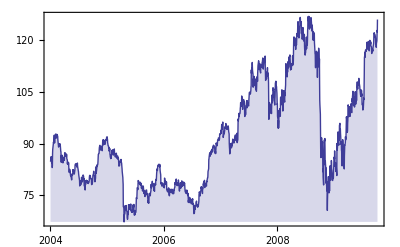

```mathematica
DateListPlot[FinancialData["IBM","Jan. 1, 2004"],Joined->True,Filling->Bottom]
```

You can also create histograms: Histogram[{x_1,x_2,…}]

```mathematica
Histogram[RandomReal[NormalDistribution[0,1],200]]
```

or bar charts: BarChart[{y_1,y_2,…}]

```mathematica
BarChart[{1,2,3,5,8}]
```

For more info check Charting and Information Visualization

Plotting lists is not confined to 2-dim plots. The function ListPlot3D generates a three-dimensional plot of a surface representing an array of height values.

```mathematica
ListPlot3D[Flatten[Table[{i,j,RandomReal[1]},{i,1,10},{j,1,10}],1]]
```

You can change the InterpolationOrder from the default (None) to your desired value

```mathematica
ListPlot3D[Table[Sin[j^2+i],{i,0,Pi,0.5},{j,0,Pi,0.5}],InterpolationOrder->3,Mesh->None]
```

#### Excercise

Plot a 3-dim ListPlot and set the INterpolationOrder to 0. What happens?

### The Structure of Plots

Required Reading:

The Structure of Graphics

In the Graphics section we already saw, that Mathematica graphics are composed of graphical primitives as well as directives. The important information is that Mathematzica represents ALL graphics in such a way. To understand this we use the command InputForm, which shows how Mathematica represents the graphics.

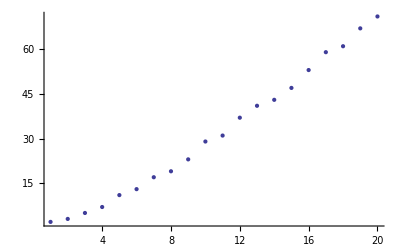

```mathematica
ListPlot[Table[Prime[n],{n,20}]]
```

```mathematica
InputForm[%]
```

Graphics[{Hue[0.67, 0.6, 0.6], Point[{{1., 2.}, 
   {2., 3.}, {3., 5.}, {4., 7.}, {5., 11.}, {6., 
   13.}, {7., 17.}, {8., 19.}, {9., 23.}, {10., 
   29.}, {11., 31.}, {12., 37.}, {13., 41.}, {14., 
   43.}, {15., 47.}, {16., 53.}, {17., 59.}, {18., 
   61.}, {19., 67.}, {20., 71.}}]}, 
 {AspectRatio -> GoldenRatio^(-1), Axes -> True, 
  AxesOrigin -> {0, Automatic}, 
  PlotRange -> Automatic, PlotRangeClipping -> 
   True}]

Each point is represented as a coordinate in a Point graphics primitive. All the various graphics options used in this case are also given.

The functions like Plot and ListPlot discussed before all work by building up Mathematica graphics objects, and then displaying them.

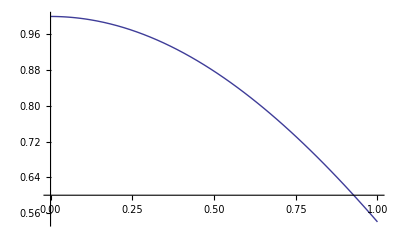

```mathematica
p=Plot[Cos[x],{x,0,1}]
```

```mathematica
InputForm[p]
```

Graphics[{{{}, {}, {Hue[0.67, 0.6, 0.6], 
    Line[{{2.040816326530612*^-8, 
     0.9999999999999998}, {0.00030671792055962676, 
     0.999999952962059}, {0.0006134154329559882, 
     0.9999998118607593}, {0.0009201129453523496, 
     0.9999995766961137}, {0.0012268104577487112, 
     0.9999992474681447}, {0.0015335079701450727, 
     0.9999988241768831}, {0.001840205482541434, 
     0.9999983068223688}, {0.0021469029949377954, 
     0.9999976954046503}, {0.002453600507334157, 
     0.9999969899237853}, {0.002760298019730519, 
     0.99999619037984}, {0.00306699553212688, 
     0.9999952967728897}, {0.0033736930445232415, 
     0.9999943091030183}, {0.003680390556919603, 
     0.999993227370319}, {0.003987088069315964, 
     0.9999920515748933}, {0.0042937855817123255, 
     0.999990781716852}, {0.004907180606505049, 
     0.9999879598134087}, {0.005213878118901411, 
     0.9999864077682722}, {0.0055205756312977725, 
     0.9999847616610509}, {0.006133970656090495, 
     0.999981187260982}, {0.0064406681684868565, 
     0.9999792589684705}, {0.006747365680883218, 
     0.9999772366145467}, {0.0073607607056759405, 
     0.9999729097232316}, {0.007667458218072303, 
     0.9999706051862474}, {0.007974155730468665, 
     0.9999682065886647}, {0.008587550755261388, 
     0.9999631272126155}, {0.009814340804846833, 
     0.9999518397438565}, {0.010121038317243194, 
     0.9999487827288979}, {0.010427735829639555, 
     0.9999456316553936}, {0.011041130854432278, 
     0.9999390473339423}, {0.012267920904017723, 
     0.9999247500021257}, {0.012574618416414085, 
     0.9999209405275962}, {0.012881315928810446, 
     0.9999170369971397}, {0.013494710953603169, 
     0.9999089477699243}, {0.014721501003188616, 
     0.9998916406611208}, {0.015028198515584977, 
     0.9998870787499535}, {0.01533489602798134, 
     0.9998824227860447}, {0.015948291052774063, 
     0.9998728287017626}, {0.017175081102359508, 
     0.9998525119201619}, {0.0196286612015304, 
     0.999807364014806}, {0.01996115644971678, 
     0.999800782731533}, {0.020293651697903155, 
     0.9997940909171952}, {0.020958642194275914, 
     0.999780375698296}, {0.022288623187021427, 
     0.999751618921088}, {0.024948585172512458, 
     0.9996888001911713}, {0.025281080420698838, 
     0.9996804505064779}, {0.025613575668885218, 
     0.9996719903040225}, {0.026278566165257974, 
     0.9996547383495797}, {0.02760854715800349, 
     0.9996189082695235}, {0.03026850914349452, 
     0.9995419436506571}, {0.0306010043916809, 
     0.9995318258008518}, {0.03093349963986728, 
     0.9995215974497156}, {0.03159849013624004, 
     0.9995008092479857}, {0.03292847112898555, 
     0.9994579068791271}, {0.035588433114476584, 
     0.9993667985495268}, {0.040908357085458646, 
     0.999163369844654}, {0.04121881843678198, 
     0.999150624770293}, {0.04152927978810532, 
     0.9991377833915501}, {0.042150202490751985, 
     0.9991118117258793}, {0.043392047896045324, 
     0.999058712797038}, {0.04587573870663201, 
     0.9989478928390847}, {0.05084312032780537, 
     0.998707766964647}, {0.05115358167912871, 
     0.9986919408100193}, {0.051464043030452045, 
     0.9986760183952207}, {0.05208496573309871, 
     0.9986438847912587}, {0.05332681113839205, 
     0.9985784625294313}, {0.05581050194897873, 
     0.9984429981464061}, {0.06077788357015209, 
     0.9981535929174875}, {0.0610822549021634, 
     0.9981350590239594}, {0.06138662623417471, 
     0.9981164326612958}, {0.06199536889819733, 
     0.9980789025354735}, {0.06321285422624258, 
     0.9980027327307043}, {0.06564782488233308, 
     0.9978459553067103}, {0.07051776619451407, 
     0.9975146525003513}, {0.07082213752652539, 
     0.9974931604928637}, {0.07112650885853669, 
     0.9974715760757075}, {0.07173525152255932, 
     0.9974281300203962}, {0.07295273685060456, 
     0.9973401290823068}, {0.07538770750669506, 
     0.997159692355681}, {0.08025764881887605, 
     0.9967810832910344}, {0.08058781788667738, 
     0.9967545588064252}, {0.08091798695447872, 
     0.9967279256639944}, {0.08157832509008137, 
     0.9966743334172932}, {0.0828990013612867, 
     0.9965658451585716}, {0.08554035390369732, 
     0.9963436542461144}, {0.09082305898851858, 
     0.9958784203303859}, {0.10138846915816112, 
     0.9948645905950501}, {0.10169660432909941, 
     0.9948333555098016}, {0.10200473950003769, 
     0.9948020259678291}, {0.10262100984191426, 
     0.9947390835256199}, {0.1038535505256674, 
     0.9946120652919996}, {0.10631863189317368, 
     0.9943534961063262}, {0.11124879462818625, 
     0.9938182324087372}, {0.12110912009821138, 
     0.9926752500155684}, {0.1424808261288228, 
     0.989866767223066}, {0.16346277092346467, 
     0.9866696832168147}, {0.18303454631887175, 
     0.9832958902441405}, {0.20425737680483996, 
     0.9792118882295561}, {0.22407003789157337, 
     0.9750011659866379}, {0.24349293774233727, 
     0.9705017706111928}, {0.26456689268366235, 
     0.9652058451810721}, {0.2842306782257526, 
     0.9598776691946022}, {0.305545518858404, 
     0.9536829950576782}, {0.32647059825508584, 
     0.9471801269181465}, {0.34598550825253294, 
     0.9407417000453775}, {0.3671514733405411, 
     0.9333536329134164}, {0.3869072690293145, 
     0.9260804551019602}, {0.408314119808649, 
     0.9177915267519796}, {0.429331209352014, 
     0.9092443456666689}, {0.44893812949614426, 
     0.900908471678687}, {0.47019610473083556, 
     0.8914794579092549}, {0.4900439105662921, 
     0.8823121923102372}, {0.5095019551657791, 
     0.8729875335501447}, {0.5306110548558273, 
     0.8624980008501449}, {0.5503099851466406, 
     0.8523624558249158}, {0.5716599705280151, 
     0.8410040423470733}, {0.5926201946734201, 
     0.8294800542026678}, {0.6121702494195903, 
     0.8184028232854835}, {0.6333713592563216, 
     0.8060367014002007}, {0.6531622996938181, 
     0.7941660404820272}, {0.6725634788953451, 
     0.7822272077414053}, {0.6936157131874332, 
     0.768939442736525}, {0.7132577780802865, 
     0.7562343256870069}, {0.7345508980637009, 
     0.7421318405713921}, {0.7544338486478805, 
     0.7286594035528418}, {0.7739270379960906, 
     0.7151713914365878}, {0.7950712824348619, 
     0.7002338783260253}, {0.8148053574743983, 
     0.686010026811993}, {0.8361904876044959, 
     0.6702947029429989}, {0.857185856498624, 
     0.654567559616441}, {0.8767710559935172, 
     0.6396364910663273}, {0.8980073105789717, 
     0.6231696603361802}, {0.9178333957651912, 
     0.6075424872220241}, {0.9372697197154413, 
     0.5919906839864062}, {0.9583570987562524, 
     0.5748650623127017}, {0.9780343083978288, 
     0.5586539712702322}, {0.9783775220102351, 
     0.5583692767165982}, {0.9787207356226415, 
     0.5580845163895298}, {0.9794071628474543, 
     0.5575147985492721}, {0.9807800172970798, 
     0.5563745750639789}, {0.9835257261963308, 
     0.5540909843984185}, {0.9890171439948328, 
     0.5495112885840302}, {0.9893603576072392, 
     0.5492245059563476}, {0.9897035712196455, 
     0.5489376586324446}, {0.9903899984444582, 
     0.5483637700311415}, {0.9917628528940837, 
     0.5472152179611288}, {0.9945085617933347, 
     0.5449150219305131}, {0.9948517754057411, 
     0.5446272082222802}, {0.9951949890181475, 
     0.544339330359368}, {0.9958814162429602, 
     0.5437633823051564}, {0.9972542706925858, 
     0.54261071783316}, {0.9975974843049922, 
     0.5423223918374163}, {0.9979406979173985, 
     0.5420340019584905}, {0.9986271251422112, 
     0.5414570306869844}, {0.9989703387546176, 
     0.5411684493623686}, {0.999313552367024, 
     0.5408798042905001}, {0.9996567659794304, 
     0.54059109550538}, {0.9999999795918367, 
     0.5403023230410169}}]}}}, 
 {AspectRatio -> GoldenRatio^(-1), Axes -> True, 
  AxesOrigin -> {0, 0.6}, PlotRange -> 
   {{0, 1}, {0.5403023230410169, 
     0.9999999999999998}}, PlotRangeClipping -> 
   True, PlotRangePadding -> {Scaled[0.02], 
    Scaled[0.02]}}]

In this case the plot p consists of 2 parts.

```mathematica
Length[p]
```

2

The first part is the all the points connected by a line to plot the sine.

```mathematica
Short[p[[1]],20]
```

{{{},{},{Hue[0.67,0.6,0.6],Line[{{2.04082×10^-8,1.},{0.000306718,1.},{0.000613415,1.},{0.000920113,1.},{0.00122681,0.999999},{0.00153351,0.999999},{0.00184021,0.999998},{0.0021469,0.999998},«141»,{0.997254,0.542611},{0.997597,0.542322},{0.997941,0.542034},{0.998627,0.541457},{0.99897,0.541168},{0.999314,0.54088},{0.999657,0.540591},{1.,0.540302}}]}}}

The second part is all the options.

```mathematica
p[[2]]
```

{AspectRatio→1/GoldenRatio,Axes→True,AxesOrigin→{0,0.6},PlotRange→{{0,1},{0.540302,1.}},PlotRangeClipping→True,PlotRangePadding→{Scaled[0.02],Scaled[0.02]}}

We can take a closer look at the structure by using some replacements in order to shorten the output. How does the InputForm look like if more than one Line is plotted? Here is an example:

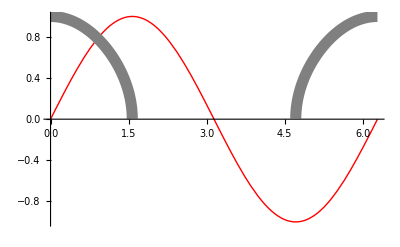

```mathematica
Plot[{Sin[x], Sqrt[Cos[x]]}, {x, 0, 2Pi},
      PlotStyle -> {{Hue[0]}, {GrayLevel[1/2], Thickness[0.02]}}]
```

```mathematica
InputForm[% //. {Line[_] -> Line["..."],
                {___?(Head[#] === Rule || 
                      Head[#] === RuleDelayed&)} -> rules}]
```

Graphics[{{rules, rules, {Hue[0.67, 0.6, 0.6], 
    Hue[0], Line["..."]}, 
   {Hue[0.9060679774997897, 0.6, 0.6], 
    GrayLevel[1/2], Thickness[0.02], Line["..."], 
    Line["..."]}}}, rules]

The graphics object can be manipulated, e.g.:

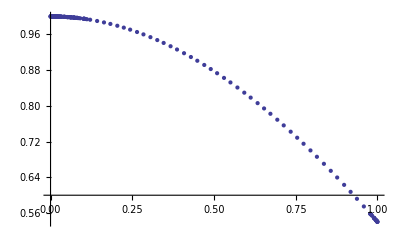

```mathematica
p/.Line->Point
```

We see, that Mathematica puts more sampling points where the plotted line has a higher curvature.

To extract the options from a graphical object we can use Options[object], which gives the options explicitly specified in a particular expression such as a graphics object. To filter out the setting for a particular option, we can use: Options[obj,name]

```mathematica
Options[p]
```

{AspectRatio→1/GoldenRatio,Axes→True,AxesOrigin→{0,0.6},PlotRange→{{0,1},{0.540302,1.}},PlotRangeClipping→True,PlotRangePadding→{Scaled[0.02],Scaled[0.02]}}

```mathematica
Options[p,PlotRange]
```

{PlotRange→{{0,1},{0.540302,1.}}}

However, components like axes, tick marks, etc. are not broken down to primitive level. The function FullGraphics gives the complete list of graphics primitives needed to generate a particular plot, without any options being used.

```mathematica
InputForm[FullGraphics[ListPlot[Table[Prime[n],{n,20}]]]]
```

Graphics[{{Hue[0.67, 0.6, 0.6], Point[{{1., 2.}, 
    {2., 3.}, {3., 5.}, {4., 7.}, {5., 11.}, {6., 
    13.}, {7., 17.}, {8., 19.}, {9., 23.}, {10., 
    29.}, {11., 31.}, {12., 37.}, {13., 41.}, {14., 
    43.}, {15., 47.}, {16., 53.}, {17., 59.}, {18., 
    61.}, {19., 67.}, {20., 71.}}]}, 
  {{GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0.2, 0.}, {0.2, 
       0.010112712429686845}}]}, 
   Text[0.2, {0.2, -0.02022542485937369}, 
    {0., 1.}], {GrayLevel[0.], AbsoluteThickness[
     0.25], Line[{{0.4, 0.}, 
      {0.4, 0.010112712429686845}}]}, 
   Text[0.4, {0.4, -0.02022542485937369}, 
    {0., 1.}], {GrayLevel[0.], AbsoluteThickness[
     0.25], Line[{{0.6000000000000001, 0.}, 
      {0.6000000000000001, 
       0.010112712429686845}}]}, 
   Text[0.6000000000000001, {0.6000000000000001, 
     -0.02022542485937369}, {0., 1.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0.8, 0.}, {0.8, 
       0.010112712429686845}}]}, 
   Text[0.8, {0.8, -0.02022542485937369}, 
    {0., 1.}], {GrayLevel[0.], AbsoluteThickness[
     0.25], Line[{{1., 0.}, 
      {1., 0.010112712429686845}}]}, 
   Text[1, {1., -0.02022542485937369}, {0., 1.}], 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.05, 0.}, {0.05, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.1, 0.}, {0.1, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.15000000000000002, 0.}, 
      {0.15000000000000002, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.25, 0.}, {0.25, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.30000000000000004, 0.}, 
      {0.30000000000000004, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.35000000000000003, 0.}, 
      {0.35000000000000003, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.45, 0.}, {0.45, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.5, 0.}, {0.5, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.55, 0.}, {0.55, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.6500000000000001, 0.}, 
      {0.6500000000000001, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.7000000000000001, 0.}, 
      {0.7000000000000001, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.7500000000000001, 0.}, 
      {0.7500000000000001, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.8500000000000001, 0.}, 
      {0.8500000000000001, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.9, 0.}, {0.9, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0.9500000000000001, 0.}, 
      {0.9500000000000001, 
       0.006067627457812106}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 0.}, {1., 0.}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 0.2}, {0.00625, 0.2}}]}, 
   Text[0.2, {-0.0125, 0.2}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 0.4}, {0.00625, 0.4}}]}, 
   Text[0.4, {-0.0125, 0.4}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 0.6000000000000001}, 
      {0.00625, 0.6000000000000001}}]}, 
   Text[0.6000000000000001, {-0.0125, 
     0.6000000000000001}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 0.8}, {0.00625, 0.8}}]}, 
   Text[0.8, {-0.0125, 0.8}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 1.}, {0.00625, 1.}}]}, 
   Text[1, {-0.0125, 1.}, {1., 0.}], 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.05}, {0.00375, 0.05}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.1}, {0.00375, 0.1}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.15000000000000002}, 
      {0.00375, 0.15000000000000002}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.25}, {0.00375, 0.25}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.30000000000000004}, 
      {0.00375, 0.30000000000000004}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.35000000000000003}, 
      {0.00375, 0.35000000000000003}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.45}, {0.00375, 0.45}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.5}, {0.00375, 0.5}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.55}, {0.00375, 0.55}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.6500000000000001}, 
      {0.00375, 0.6500000000000001}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.7000000000000001}, 
      {0.00375, 0.7000000000000001}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.7500000000000001}, 
      {0.00375, 0.7500000000000001}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.8500000000000001}, 
      {0.00375, 0.8500000000000001}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.9}, {0.00375, 0.9}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.125], 
    Line[{{0., 0.9500000000000001}, 
      {0.00375, 0.9500000000000001}}]}, 
   {GrayLevel[0.], AbsoluteThickness[0.25], 
    Line[{{0., 0.}, {0., 1.}}]}}}]

Now we see, how the axes are composed, how the ticks are placed and drawn, etc. During the course, we will make use of our understanding of the structure of graphics and plots to study and manipulate them.

You can create other kinds of graphical images in Mathematica by building up your own graphics objects. Since graphics objects in Mathematica are just symbolic expressions, you can use all the standard Mathematica functions to manipulate them.

### Function Evaluation

It is critically important that the function to be plotted produces a real number when its variable is replaced by a numerical value.  If your function contains unevaluated parameters, it cannot be plotted.  Perhaps the most common error encountered using plotting commands is to leave some constant in symbolic form.

```mathematica
Plot[A Exp[-k x]/.{k->0.2},{x,0,10}]
```

We did not specify a numeric value of A, so Mathematica could not produce a Plot of our function.

Sometimes Mathematica complains that the function is not a machine - size real number, it isn' t even a definite number of any kind.  Nevertheless, Mathematica will plot whatever it can, useful or not.  In this case, it simply produces a set of axes with default ranges and increments because that is the only part of the command it can evaluate.

If we specify A, a more meanigful Plot will show up.

```mathematica
Plot[A Exp[-k x]/.{k->0.2,A->2.},{x,0,10}]
```

Note, that we provided A and k via replacement rules. Of course we could have assigned values liek A=2 and k=0.2. But this would result in a persistent definition of k and A until we Clear theri values again. It is very easy to loose track over already defined expressions, and one should keep their number small. We will learn more about localication later.

Plot can also swallow functions that we defined ourselves:

```mathematica
Clear[f]
f[x_]:=Sin[7.32x]Exp[x/2.]
```

```mathematica
Plot[f[x],{x,0,5}]
```

We just have to make sure, that the function gives numerical values once arguments are filled in. To be more specific, the help page on Plot reads:
Plot has attribute HoldAll, and evaluates f only after assigning specific numerical values to x.

This is important if the function f involves some delayed assignments, e.g.:

```mathematica
Clear[g]
g[x_] := y[x]/.NDSolve[{y''[x]==x Sin[x], y[0]==0, y'[0]==1},y[x],{x,0,10}]
```

The following fails miserably, because when Plot assigns x-values to g[x], it is not yet set, due to the delayed assignment. Mathematica does not even know wheteher g[x] will be a number or a symbol.

```mathematica
Plot[g[x], {x,0,5}]
```

We need to make sure that g[x] is evaluated first. This can be forced by Evaluate

```mathematica
Plot[Evaluate[g[x]], {x,0,5}]
```

Here is another example of this behavior. Imagine we want to plot a list of functions together in one plot. We will use a programmatic approach to set up the list of functions, e.g. to create alist of trigonometric functions we can use Table::

```mathematica
Table[i[x],{i,{Sin,Cos,Tan,Sinh,Cosh,Tanh}}]
```

This is saving us some typing especially when we use a complicated but repetetive argument like:

```mathematica
Table[i[√x-x/2+x^2],{i,{Sin,Cos,Tan,Sinh,Cosh,Tanh}}]
```

Again, the point is, that Plot has the Attribute HoldAll and leaves its arguments, i.e. the functions to plot unevaluated. This means the Plot is not seeing a list of trigonometric functions to plot, but a single function (in this case the Table function). Hence only one styling primitive is set up to draw the plot and so all functions use the same PlotStyle. If the list structure is not manifest, no separate styling is provided

```mathematica
Plot[Table[i[x],{i,{Sin,Cos,Tan,Sinh,Cosh,Tanh}}],{x,-π/2,π/2}]
```

Use Evaluate to make the list structure manifest, i.e. to transform the Table command into a list of function:

```mathematica
Plot[Evaluate@Table[i[x],{i,{Sin,Cos,Tan,Sinh,Cosh,Tanh}}],{x,-π/2,π/2}]
```

A list of unevalueted constructs gets different PlotStyles. In our example the regular functions get one style, the hyperbolic ones ghet the second style:

```mathematica
Plot[{Table[i[x],{i,{Sin,Cos,Tan}}],Table[i[x],{i,{Sinh,Cosh,Tanh}}]},{x,-π/2,π/2}]
```

#### Excercises

Execute the following two commands and explain the difference
Plot[ Evaluate[ Table[LegendreP[n, x], {n, 0, 10}]], {x, -1, 1}];
Plot[  Table[LegendreP[n, x], {n, 0, 10}], {x, -1, 1}];

What is the difference between:

Plot[{Evaluate@Table[i[x],{i,{Sin,Cos,Tan}}],Evaluate@Table[i[x],{i,{Sinh,Cosh,Tanh}}]},{x,-π/2,π/2}]

and

Plot[Evaluate@{Table[i[x],{i,{Sin,Cos,Tan}}],Table[i[x],{i,{Sinh,Cosh,Tanh}}]},{x,-π/2,π/2}]
Explain the difference,

Define a function f(p)= ∑_(n=0)^p ((-1)^n x^(2n))/(∏_(m=1)^n (2m)^2)
that will allow you to evaluate the expression for arbitrary integer values of p. Use Table to generate a list of partial sums  for p=1,2,…10. Then use Plot to display the partial sums for 0≤x≤10. Be sure to wrap the first argument of Plot with Evaluate. See what happens if you do not use evaluate

### Options for Graphics

Required Reading 

Options for Graphics
Graphics Annotation & Appearance

We already encountered Mathematica functions that worked differently, depending on user supplied Options. Plot is one of the main examples for this feature. With Options we can control the output and behavior of our Plots significantly.

```mathematica
Options[Plot]//Length
```

```mathematica
Options[Plot]
```

#### Axis labels and titles

The simplest labeling uses AxesLabel for the axes and PlotLabel for the entire figure.  One simply replaces the defaults by a list of strings for AxesLabel, where the first label is for the x-axis and the second for the y-axis, or by a single string for PlotLabel.

```mathematica
Plot[Gamma[x],{x,-5,5},
	AxesLabel->{"x", "Γ[x]"}, PlotLabel->"Gamma Function"]
```

You can also  use Frame→True to draw a frame around the figure and FrameLabel→{bottom, left, top, right} to place labels outside the edges of the figure.  Note that FrameLabel expects lists with either 2 or 4 elements.  Thus, if we do not want to label the right side we can include a blank string with the 3 labels we do want, or we can give 2 labels to FrameLabel and use PlotLabel for the top

```mathematica
Plot[Gamma[x],{x,-5,5}, Frame->True,FrameLabel->{"x", "Γ[x]","Gamma Function"," "}]
```

However, the format specification for Labels changed in a recent Version change. Mathematica understands the old clockwise specification, but the Help page for FrameLabel explains the new format:
  FrameLabel->{{left,right},{bottom,top}} specifies labels for each of the edges of the frame.

```mathematica
Plot[Gamma[x],{x,-5,5}, Frame->True,FrameLabel->{{ "Γ[x]",""},{"x","Gamma Function"}}]
```

Mathematica automatically uses TraditionalForm when writing mathematical expressions.

```mathematica
Plot[Sin[x],{x,-π,π},PlotLabel->Sin[x]]
```

We did not give an explicit String! Note that TraditionalForm[Sin[x]]=sin(x). Here a few examples:

```mathematica
TraditionalForm[Sin[x]]
```

```mathematica
Plot[BesselJ[0,x],{x,0,50},PlotLabel->BesselJ[0,x]]
```

```mathematica
Plot[Abs[z],{z,0,50},PlotLabel->Abs[z]]
```

Excercise: Plot a Sin[x] between 0 and 2π in a framed plot. Put labels on the right and top frame axis, but no labels on the left and bottom axis.

Excercise : Duplicate the above Plot now with only labels on the left and on the right. .

#### AxesStyle

AxesStyle is an option for graphics functions which specifies how axes should be rendered.

Styles can be specified using graphics directives such as Thick, Red, and Dashed as well as Thickness, Dashing and combinations given by Directive.

```mathematica
Plot[Sinc[x],{x,0,10},AxesStyle->Orange]
```

```mathematica
Plot[Sinc[x],{x,0,10},AxesStyle->Directive[Orange,12]]
```

Specify the style of each axis:

```mathematica
Plot[Sinc[x],{x,0,10},AxesStyle->{Directive[Red,12],Blue}]
```

```mathematica
Graphics3D[Cylinder[],Axes->True,AxesStyle->{Red,Green,Blue}]
```

Use Arrowheads to style the axes:

```mathematica
Plot[x^3,{x,-1,1},AxesStyle->Arrowheads[{-0.05,0.05}]]
```

TicksStyleaffects ticks and tick labels,but nothing else:

```mathematica
Plot[2Sin[x],{x,0,10},AxesLabel->{x,y},PlotLabel->2Sin[x],TicksStyle->Orange]
```

To change style of frames use FrameStyle. FrameStyle->style specifies the style to use for all sides of the frame. FrameStyle->{{left, right}, {bottom, top}} specifies what style to use for which side.

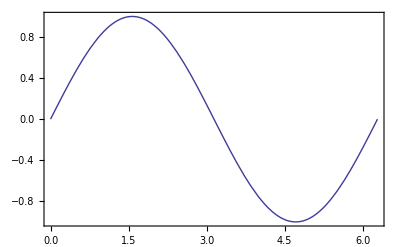

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,FrameStyle->{{Thick,Directive[Thick,Dashed]},{Blue,Red}}]
```

In the example we used Directive[Thick, Dashed] to group several styling primitives together to be used for the right frame side. This is important to unambigiously specify the styles for each side:

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,FrameStyle->{{Thick,Thick,Dashed},{Blue,Red}}]
```

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,FrameStyle->{{Thick,Dashed,Thick},{Blue,Red}}]
```

Mathematica can not decide how to spread three primitives to 2 sides and ignores all of them.

#### Ticks

To specify the tick marks for an axis we use the option Ticks. The follwoing general values can be given to Ticks: None, Automatic,  and {xticks, yticks, …}. With the Automatic setting, tick marks are usually placed at points whose coordinates have the minimum number of digits in their decimal representation.

```mathematica
Plot[Sin[x],{x,0,2Pi},Ticks->None]
```

```mathematica
Plot[Sin[x],{x,0,2Pi},Ticks->{{0,2,4,6},{-1,0,1}}]
```

If we don't specify, the tick mark labels are given as the numerical values of the tick mark positions.

```mathematica
Plot[Sin[x],{x,0,2Pi},Ticks->{{0,Pi/2,Pi,3Pi/2,2Pi},{-1,0,1}}]
```

Alternatively you can give tick mark position and label independantly. The syntax is {{x_1,label_1},{x_2,label_2},…}. Note the braces:

```mathematica
Plot[Sin[x],{x,0,2Pi},Ticks->{{{Pi/2,"Max"},{3Pi/2,"Min"}},{-1,0,1}}]
```

You can also control the length of each tick with scaled lengths

```mathematica
Plot[Sin[x],{x,0,2Pi},Ticks->{{{Pi/2,"Max",0.01},{3Pi/2,"Min",0.03}},{-1,0,1}}]
```

Specify tick marks with scaled lengths in positive and negative directions:

```mathematica
Plot[Sin[x],{x,0,2Pi},Ticks->{{{Pi/2,"Max",{0.01,0.05}},{3Pi/2,"Min",{0.03,0}}},{-1,0,1}}]
```

You have full control over the styling of all tick marks and their labels. {{x_1,label_1,len_1,style_1},…}

```mathematica
Plot[Sin[x],{x,0,2Pi},Ticks->{{{Pi/2,"Max",{0.01,0.05},Directive[Red,Thick]},{3Pi/2,"Min",{0.03,0},Directive[Green,Thickness[0.05]]}},{-1,0,1}}]
```

You can also provide a function to calculate ticks on the run. This function is to be applied to x_min, x_max to get the tick mark specification.

```mathematica
ticks[min_,max_]:=Table[If[EvenQ[i],{i,i,.06,Red},{i,i,.02,Blue}],{i,Ceiling[min],Floor[max],1}]
```

```mathematica
Graphics[Circle[{0,0},4],Axes->True,Ticks->ticks]
```

You can do the same customization also with FrameTicks.

```mathematica
Plot[Sin[x],{x,0,10},Frame->True,FrameTicks->{{{0,0°},{Pi,Style[180°,Red],{0.01,0},Red},{2Pi,360°},{3Pi,540°}},{-1/2,1/2}}]
```

Excercise: Simulate a log-log plot of ⅇ^x between 1 and 10 by plotting x and using costum tick marks.

#### Grid lines

GridLines is an option for two-dimensional graphics functions that specifies grid lines.

```mathematica
Plot[Gamma[x],{x,-5,5}, Frame->True,FrameLabel->{{ "Γ[x]",""},{"x","Gamma Function"}},GridLines->Automatic]
```

GridLines can be specified explicitely using {xgrid, ygrid}

```mathematica
Plot[Gamma[x],{x,-5,5}, Frame->True,FrameLabel->{{ "Γ[x]",""},{"x","Gamma Function"}},
GridLines->{{-4,-2,0,2,4},{-5,0,5}}]
```

#### Plot Range

PlotRangeis an option for graphics functions that specifies what range of coordinates to include in a plot.

Normally, plot functions drop outlying points, which is equivalent to PlotRange->Automatic:

```mathematica
{Plot[1/x,{x,0.01,1}],Plot[1/x,{x,0.01,1},PlotRange->Automatic]}
```

PlotRange->All shows all of the points:

```mathematica
Plot[1/x,{x,0.01,1},PlotRange->All]
```

```mathematica
{Plot3D[Exp[-x^2-y^2],{x,-4,4},{y,-4,4},PlotRange->All,PlotLabel->PlotRange->All],Plot3D[Exp[-x^2-y^2],{x,-4,4},{y,-4,4},PlotRange->Automatic,PlotLabel->PlotRange->Automatic]}
```

You can also give explicit limits for all axes using {{x_min,x_max},{y_min,y_max}}

```mathematica
Plot[x^2,{x,-4,4},PlotRange->{{-3,6},{-5,15}}]
```

#### AspectRatio

AspectRatio  is an option for Graphics and related functions which specifies the ratio of height to width for a plot.

Automatic can be given to choose the ratio from the actual plot values:

```mathematica
{Plot[Sqrt[1-x^2],{x,0,1}],Plot[Sqrt[1-x^2],{x,0,1},AspectRatio->Automatic]}
```

Specify the height-to-width ratio of a graphic by numerical values:

```mathematica
{ParametricPlot[{Cos[u],1/10Sin[u]},{u,0,2Pi}],
ParametricPlot[{Cos[u],1/10Sin[u]},{u,0,2Pi},AspectRatio->1/2]}
```

#### PlotStyle

PlotStyle is an option for plotting and related functions that specifies styles in which objects are to be drawn.

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle->Red]
```

You can specify multiple Style directives for one Plot as a list

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle->{Red,Thick,Dashed}]
```

If you plot multiple functions simultaneously you can give the style directives for each function seperately in a list

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotStyle->{Red,Green,Blue}]
```

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotStyle->{Red,{Thin,Green,Dotted},{Blue,DotDashed}}]
```

Consult Graphics Directives for a list of possible directives.

#### PlotPoints

PlotPoints is an option for plotting functions that specifies how many initial sample points to use. Mathematica then uses adaptive sampling, increasing the number of samples near interesting features, but it is still possible to miss something. By increasing PlotPoints, you can make Mathematica sample your function at a larger number of points. Of course, the larger you set PlotPoints to be, the longer it will take Mathematica to plot any function, even a smooth one.

```mathematica
Plot[Sinc[x],{x,0,10},Mesh->All,MaxRecursion->0,PlotPoints->15]
```

```mathematica
Plot[Sinc[x],{x,0,10},Mesh->All,MaxRecursion->0,PlotPoints->40]
```

Mesh is an option for plotting functions that specifies what mesh should be drawn and MaxRecursions specifies how many recursive subdivisions can be made. By setting it to 0 we prohibit any further adaptive sampling. When we increase the value we can see how Mathematica adds more points around interesting features.

```mathematica
Plot[Sinc[x],{x,0,10},Mesh->All,MaxRecursion->1,PlotPoints->20]
```

```mathematica
Plot[Sinc[x],{x,0,10},Mesh->All,MaxRecursion->2,PlotPoints->20]
```

#### More options

There are still more options for plots. We will not cover all of them but give examples of some.

Mathematica uses a default ClippingStyle when curves are cut off due to a PlotRange setting.Setting ClippingStyle to Automatic draws a dashed line where a curve is cut off.

```mathematica
Plot[{Sin[x^2], Cos[x^2]},{x,0,3},PlotRange->0.9,ClippingStyle->Automatic]
```

Setting ClippingStyle to a list defines the style for the parts cut off at the bottom and top.

```mathematica
Plot[{Sin[x^2], Cos[x^2]},{x,0,3},PlotRange->0.9,ClippingStyle->{Automatic,Directive[Thick,Green]}]
```

Filling is an option for ListPlot, Plot, Plot3D and related functions which specifies what filling to add under points, curves and surfaces

```mathematica
Table[Plot[Sin[x],{x,0,2Pi},Filling->f],{f,{Top,Bottom,Axis,0.3}}]
```

Giving Filling->{m} fills to the m^th object and {i_1->p_1,i_2->p_2,…} fill from object i_k to p_k

```mathematica
Plot[{Sin[x^2], Cos[x^2],Sin[x]Cos[x]},{x,0,3},Filling->{2}]
```

```mathematica
Plot[{Sin[x^2], Cos[x^2],Sin[x]Cos[x]},{x,0,3},Filling->{1->{3}}]
```

Again you can also provide style directive:

```mathematica
Plot[{Sin[x^2], Cos[x^2],Sin[x]Cos[x]},{x,0,3},Filling->{1->{{3},Directive[Red,Opacity[0.6]]}}]
```

RegionFunction is an option for plotting functions which specifies the region to include in the plot drawn. You can provide any funtion:

```mathematica
Plot[{Sin[x^2], Cos[x^2],Sin[x]Cos[x]},{x,0,3},Filling->{1->{{3},Directive[Red,Opacity[0.6]]}},RegionFunction->Function[{x,y},1≤x≤2.5]]
```

```mathematica
Plot[{Sin[x^2], Cos[x^2],Sin[x]Cos[x]},{x,0,3},Filling->{1->{{3},Directive[Red,Opacity[0.6]]}},RegionFunction->Function[{x,y},Mod[x,2]<1]]
```

#### Excercise

Plot cos(x) from 0 to 10 and make the plot framed, with a dashed, brown frame.

Add grid lines for x={1,3,7}.

Make the tick labels italic and red.

Label the plot.

### Editing Mathematica Graphics - Drawing Tools

Required Reading
Editing Mathematica Graphics
Drawing Tools

Mathematica offer a set of drawing tools to alter the appearance of a plot. This is convenient if you want to add labels, sketch something in the plot, etc. However, after deleting the plot, there is no way to recover what you did before.

#### Excercises

Graphically find the first three solutions to the equation Cos[x]==Log[x/(x-1)]

### Editing Mathematica Graphics - Programmatically

Now we will make use of our knowledge about the internal representation of graphical objects within Mathematica.

At first we will show a very simple example with a stunning effect though. Take a parametric plot.

```mathematica
pl=ParametricPlot[Evaluate[
     (Exp[Cos[σ]] -Cos[4 σ] + Sin[σ/12]^7) {Cos[σ], Sin[σ]}],
     {σ, 0, 2Pi}, AspectRatio -> Automatic, Axes -> None]
```

Replacing the Line primitive with a polygon leads to a closed and filled polygon.

```mathematica
pl/.Line->Polygon
```

The coordinates of the points are at level {1, 1, 3, 2, 1}. Multiplying all coordinates with 1/2 effectively shrinks the polygon. We plot the shrinked version together with the original one:

```mathematica
Show@{pl/.Line->Polygon,Graphics@Polygon[pl[[1,1,3,2,1]]*0.5]}
```

Now we progressively shrink the polygon and change the color to produce a beautifull filling effect:

```mathematica
Graphics@Table[{Hue[i],Polygon@(pl[[1,1,3,2,1]]*i)},{i,1,0.01,-0.01}]
```

For a little more complex example consider the cosine plot:

```mathematica
pl=Plot[Cos[x], {x, 0, 2Pi},PlotPoints->60,MaxRecursion->0]
```

We want to replace the plotted line by a connected set of rectangles. We know that the plot consists of styling options and a Line[ many points ] part.

```mathematica
InputForm[% //. Line[_] -> Line["..."]]
```

To extract the points look at the above input form to find the level where the Line command sits:

```mathematica
pl[[1,1,3,2,0]]
```

Level 0 of the expression is the head, level 1 its argument, in our case the list of points.

```mathematica
points=pl[[1,1,3,2,1]];
```

To draw a rectangle we need the coordinates of the lower lft and the upper right corner. These are two neighboring points from our list. We can split the list to make seperate rectangles:

```mathematica
splitpoints=Partition[points,2];
```

Now we create a list of rectangles.

```mathematica
rectangles=Table[Rectangle[splitpoints[[i]][[1]],splitpoints[[i]][[2]]],{i,1,Length@splitpoints}];
```

```mathematica
Graphics[rectangles]
```

It would be nice if we had no gaps. We can create the partition with overlaps:

```mathematica
splitpoints=Partition[points,2,1];
```

```mathematica
rectangles=Table[Rectangle[splitpoints[[i]][[1]],splitpoints[[i]][[2]]],{i,1,Length@splitpoints}];
```

We can draw it together with the original line:

```mathematica
Show[{pl,Graphics[rectangles]}]
```

Since we already saw how to construct the rectangles from the original plot, we can also use our phantasy to style it a little more. Lets color the rectangles according to their x-vaue:

```mathematica
rectangles=Table[{Hue[(splitpoints[[i]][[1,1]]+splitpoints[[i]][[2,1]])/(4Pi)],Rectangle[splitpoints[[i]][[1]],splitpoints[[i]][[2]]]},{i,1,Length@splitpoints}];
```

```mathematica
Show[{pl,Graphics[rectangles]}]
```

Instead of one rectangle we now draw a set of shrinking rectangles on top of each other. Mathematica offers a set of transformation functions which are very convenient

```mathematica
rectangles=Table[Table[{Hue[(splitpoints[[i]][[1,1]]+splitpoints[[i]][[2,1]])/(4Pi)j],Scale[Rectangle[splitpoints[[i]][[1]],splitpoints[[i]][[2]]],j]},{j,2,0.1,-0.1}],{i,1,Length@splitpoints}];
```

```mathematica
Show[{pl,Graphics[rectangles]}]
```

We can also rotate the rectangles:

```mathematica
rectangles=Table[Table[{Hue[(splitpoints[[i]][[1,1]]+splitpoints[[i]][[2,1]])/(4Pi)j],Rotate[Scale[Rectangle[splitpoints[[i]][[1]],splitpoints[[i]][[2]]],j],j-2]},{j,2,0.1,-0.1}],{i,1,Length@splitpoints}];
```

```mathematica
Show[{pl,Graphics[rectangles]}]
```

Puttin all together in a single command:

```mathematica
Remove[convertToRectangles];
convertToRectangles[plot_]:=Graphics[Table[Table[{Hue[(#[[i]][[1,1]]+#[[i]][[2,1]])/(2 Options[plot,PlotRange][[1,2,1,2]])j],Rotate[Scale[Rectangle[#[[i]][[1]],#[[i]][[2]]],j],j-2]},{j,2,0.1,-0.1}],{i,1,Length@#}]&[Partition[plot[[1,1,3,2,1]],2,1]]]
```

Test:

```mathematica
Plot[Sin[t]*Cos[12t] ,{t,1,3.1}]
```

```mathematica
convertToRectangles[%]
```

All together:

```mathematica
Show[%%,%]
```

-Graphics-

### Combining Plots

Required Reading

Redrawing and Combining Plots
Combining Graphics
Grids, Rows, and Columns
Insetting Objects in Graphics

You can use the Show to either show a plot with an alternative set of options:
Show[graphics,options] or you can combine several plots in one.
Show[g_1,g_2,…] shows several graphics combined.

```mathematica
Plot[Sin[x^2]/x,{x,0,10}]
```

Now we change the options a little:

```mathematica
Show[%,PlotRange->{{8,10},{-.3,.3}},AxesOrigin->{8.0,0}]
```

```mathematica
{DensityPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3}],ContourPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3},ContourShading->None]}
```

```mathematica
Show[%[[1]],%[[2]]]
```

When combining two plots, Mathematica again produces a Graphics object with the already known structure:

```mathematica
i1 = ParametricPlot[
Evaluate[{+2, +3} + (-1 +0.5 Sqrt[Abs[φ]]) {Cos[φ], Sin[φ]}],
                        {φ, -4Pi, 4Pi}]

i2 = ParametricPlot[
Evaluate[{-5, -5} + (-1 - 3 Log@Sqrt[Abs[φ]]) {Cos[φ], Sin[φ]}],
                        {φ, -3Pi, 3Pi}, PlotPoints -> 500]
```

```mathematica
Show[i1, i2, PlotRange -> All]
```

The resulting Graphics-object consists of two separate lines along with the values of the options. The two lines are also contained in List, which is necessary to pass on any graphics directives, such as thickness and color.

```mathematica
InputForm[% /. {Line[_] ->"longLine"}]
```

When you combine multiple plots using Show without any further options, then Mathematica uses the PlotRange from the first plot! This might cut off interesting parts of the remaining plots. The order is important here.

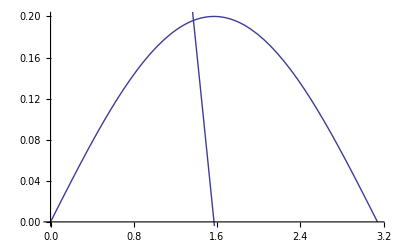
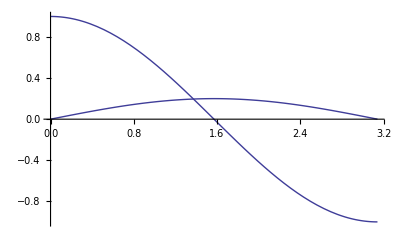

```mathematica
{Show[{Plot[0.2Sin[x],{x,0,Pi}],Plot[Cos[x],{x,0,Pi}]}],Show[{Plot[Cos[x],{x,0,Pi}],Plot[0.2Sin[x],{x,0,Pi}]}]}
```

You can also Inset one graphic object into another

```mathematica
in=Plot[Cos[x],{x,-3 Pi,3Pi},ImageSize->100,Frame->True];
Plot[Sin[x] /x,{x,-3 Pi,3Pi},Epilog->Inset[in,{6,0.6}]]
```

You can arrange multiple plots in Grids, Rows and Columns

GraphicsRow[{g_1,g_2,…}] generates a graphic in which the g_i are laid out in a row.

GraphicsColumn[{g_1,g_2,…}]generates a graphic in which the g_i are laid out in a column, with g_1 above g_2, etc.

GraphicsGrid[{{g_11,g_12,…},…}]generates a graphic in which the g_ij are laid out in a two-dimensional grid.

```mathematica
$TrigFunctions={Sin,Cos,Sec,Csc};
Table[Plot3D[Abs[f[x+I y]],{x,-2,2},{y,-2,2},MeshFunctions->Function@@@{{{x,y,z},Re[f[x+I y]]},{{x,y,z},Im[f[x+I y]]}},MeshStyle->{Orange,Green},PlotLabel->f,Ticks->None],{f,$TrigFunctions}];
GraphicsRow[%]
GraphicsColumn[%%]
GraphicsGrid[{%%%[[1;;2]],%%%[[3;;4]]}]
```

#### Excercise

Create a 3x2 array of plots. Adapt the ImageSize so that all plots fit on your screen.

What happens when you use Show to combine the two plots:
Plot[x,{x,0,5}] and Plot[x,{x,-5,0}]. pay attention to the resulting x- and y-range.

Use GraphicsRow to plot the two plots from the excercise before in a row and draw frames around each plot.

Instead of GraphicsRow use Row. What are the differences?

Plot a function of your choice and write the function in a corner of the plot.

### Logarithmic Plots

Plot uses a decimal axis scale. You can use logarithmic scales using the following commands:
LogPlot, LogLinearPlot, LogLogPlot

```mathematica
f[x_]:=Exp[-x]+4 Exp[-2x]
```

```mathematica
{Plot[f[x],{x,1,6}],LogPlot[f[x],{x,1,6}],LogLinearPlot[f[x],{x,1,6}],LogLogPlot[f[x],{x,1,6}]}
```

LogPlot effectively generates a curve based on Log[f], but with tick marks indicating the values of the underlying function f.

```mathematica
{LogPlot[x^Sin[x],{x,0,10}],Plot[Log[x^Sin[x]],{x,0,10},AxesOrigin->{0,-1.5}]}
```

Mathematica uses a special set of rules to determine which ticks to draw in logarithmic plots. The result may not be what you might want for publication ready plots. Sometimes you will need to use custom ticks to produce the desired results. Sometimes it is just the tick mark labels that are not what you might want.

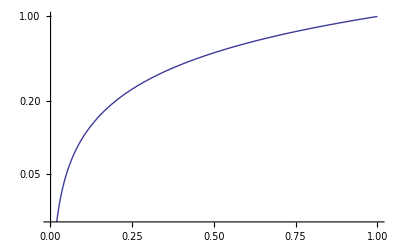

```mathematica
LogLogPlot[x,{x,0.001,1}]
```

For ranges of more than 6 dex the ticks and labels are placed very unconveniently:

```mathematica
LogLogPlot[x,{x,1,10^7}]
```

```mathematica
LogLogPlot[x,{x,1,10^6}]
```

Take a look at the 'true' coordinates of a log-plot.

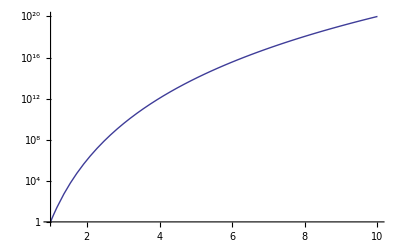

```mathematica
LogPlot[x^20,{x,1,10}]
```

The y-value 10^20is drawn at the plot y-value of 46.051701859880914.

```mathematica
InputForm[Options[LogPlot[x^20,{x,1,10}]]]//Short[#,10]&
```

{Ticks -> {Automatic, {{0, 1}, {9.210340371976184, Superscript[10, 4]}, {18.420680743952367, Superscript[10, 8]}, {27.631021115928547, Superscript[10, 12]}, {36.841361487904734, Superscript[10, 16]}, {46.051701859880914, Superscript[10, 20]}, {7.013915474810528, "", {0.00375, 0.}, {Thickness[0.001]}}, {<<4>>}, <<34>>, {45.46399519177896, "", {0.00375, 0.}, {Thickness[0.001]}}, {45.64628675052279, "", {0.00375, 0.}, {Thickness[0.001]}}, {45.80041600262042, "", {0.00375, 0.}, {Thickness[0.001]}}, {45.93393132414641, "", {0.00375, 0.}, {Thickness[0.001]}}}}, <<14>>}

This is ln(10^20)

```mathematica
Log[10^20]//N
```

46.0517

Imagine you want to write some text in the plot. You can use Epilog to do this, but beware the coordinates:

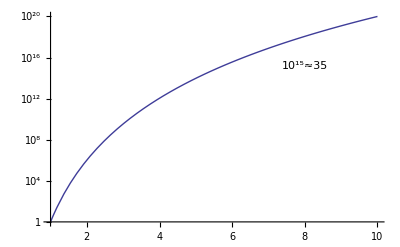

```mathematica
LogPlot[x^20,{x,1,10},Epilog->Text["10^15≈35", {8,35}]]
```

#### Excercises

Plot the following list of Points logarithmically: Table[Power10,i],{i,1,10}]

Plot f(x)= sin(x)exp(x) from x=[0,100]

Use Show to combine two log-log Plots.

### Plotting a function of two variables

Required Reading

Density and Contour Plots
Parametric Plots

An explicit function of two independent variables can be displayed using Plot3D.  The basic syntax is Plot3D[f,{x,xmin,xmax},{y,ymin,ymax}].

```mathematica
Plot3D[Im[ArcSin[(x+I y)^4]],{x,-2,2},{y,-2,2},PlotPoints->50,PlotStyle->Directive[Pink,Specularity[White,50],Opacity[0.8]]]
```

Contour or density plots often prove very useful in locating extrema, ridges, or other important features of functions of two or more dimensions.  These plots can also help in finding starting points for numerical solution of equations.

DensityPlot[f,{x,x_min,x_max},{y,y_min,y_max}] make a density plot of f
ContourPlot[f,{x,x_min,x_max},{y,y_min,y_max}] make a contour plot of f as a function of x and y

```mathematica
DensityPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2},ColorFunction->ColorData["SolarColors"]]
```

Move with the mouse over the contours in the following contour plot. The default style is to add a tooltip to indicate the contour level.

```mathematica
ContourPlot[Sin[x] Sin[y],{x,-2,2},{y,-2,2}]
```

```mathematica
ContourPlot[Sin[x]Sin[y],{x,-2,2},{y,-2,2},ContourLabels->True]
```

A speciality is the ability ofg contour plot to plot implicit plots,

```mathematica
ContourPlot[x^2+y^2==1,{x, -1,1},{y,-1,1}]
```

```mathematica
ContourPlot[Sin[x] Sin[y]==0.2,{x,-3,3},{y,-3,3}]
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u.

#### Excercises

Plot the curve described by the parametric equations {x=r (1-sin(t)), y=r (1-cos(t))} for the interval {t,-2π,2π}.

Use Plot3D to draw the surface f(x,y)=Exp(-y^2)sin(x)-1 in the box region -2≤x≤2, -2≤y≤2.Then use ContourPlot to display the surface contours. Use ContourPlot to you visualize the solution f(x,y)=-0.9?

### Special Plots

Required Reading

Some Special Plots

The Plot command is used to plot functions in the form y=f[x]. Mathematica also understands parametrized formulation of functions. ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u.

This is the parameter form of a circle:

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

Another plot with a more random appearance

```mathematica
ParametricPlot[Evaluate @ 
Table[Sum[Sin[i + j] Cos[i t + Pi Sin[i]], 
          {i, 17}], {j, 1, 2}], {t, 0,2 Pi}, 
   PlotRange -> All, Frame -> True, PlotPoints -> 5000,
   Axes -> False, AspectRatio -> Automatic]
```

Plot multiple functions

```mathematica
ParametricPlot[{{Sin[u],Sin[2u]},{1/2Cos[u],1/2Sin[u]}},{u,0,2Pi}]
```

An interesting feature is the capability to plot parametric regions: ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}]

```mathematica
ParametricPlot[{r Cos[t],r Sin[t]},{t,0,2Pi},{r,0.5,1},Mesh->False]
```

```mathematica
ParametricPlot[Evaluate[
     (Exp[Cos[σ]] - 2Cos[4 σ] + Sin[σ/12]^5) {Cos[σ], Sin[σ]}],
     {σ, 0, 2Pi}, AspectRatio -> Automatic, Axes -> None]
```

Remember our function to replace points with scaled and rotated rectangles? ParametricPlot also produces a list of points to be connected with lines, hence:

```mathematica
convertToRectangles[%]
```

The 3-dim counterpart is of course ParametricPlot3D[{f_x,f_y,f_z},{u,u_min,u_max}].

```mathematica
pl=ParametricPlot3D[{(2+Cos[8u])Cos[u],(2+Cos[8u])Sin[u],Sin[8u]},{u,0,2Pi}]
```

convertToRectangles ??

In 3-dim a rectangle becomes a cuboid. The upgrade of our playground routine is more or less straight forward. We omitted the rotation part and used oppacity to make the inner 2 cuboids visible. However, this makes the rendering quite slow.

```mathematica
Remove[convertToCuboids]
convertToCuboids[plot_]:=Graphics3D[Table[Table[{Opacity[1/j],Hue[i/(Length@#)j],Scale[Cuboid[#[[i]][[1]],#[[i]][[2]]],j]},{j,3,1,-1}],{i,1,Length@#}]&[Partition[plot[[1,1,3,2,1]],2,1]]]
```

```mathematica
convertToCuboids[pl]
```

Another example from the Mathematica Guide Books:

```mathematica
f = (2 + Cos[u/2] Sin[t] - Sin[u/2] Sin[2t]) Cos[u];
g = (2 + Cos[u/2] Sin[t] - Sin[u/2] Sin[2t]) Sin[u];
h = Sin[u/2] Sin[t] + Cos[u/2] Sin[2t];

ParametricPlot3D[{f, g, h},
                 {t, 0, 2Pi}, {u, 0, 2Pi},ColorFunction->Function[{x,y,z,u,t},Hue[(t + u)/(4Pi)]],Boxed -> False,Axes -> None]
Remove[f,g,h,pl]
```

PolarPlot[r,{θ,θ_min,θ_max}]  generates a polar plot of a curve with radius r as a function of angle θ.

```mathematica
PolarPlot[Sin[Pi t^2],{t,0,Pi}]
```

ListPolarPlot[{r_1,r_2,…}] plots points equally spaced in angle at radii r_i.

```mathematica
butterfly[λ_][p_,o___]:=ListPolarPlot[Table[{θ,(Exp[Cos[θ]]-2Cos[4θ])Sin[λ θ]^4},{θ,0,2Pi,p}],o,PlotRange->All,PlotStyle->PointSize[Tiny]]
```

```mathematica
butterfly[99999999][0.00055]
```

```mathematica
butterfly[99999999][0.0005]
```

SphericalPlot3D[r,θ,ϕ]generates a 3D plot with a spherical radius r as a function of spherical coordinates θ and ϕ.

```mathematica
SphericalPlot3D[ϕ+ Sin[7θ],θ,ϕ]
```

SphericalPlot3D[r,{θ,θ_min,θ_max},{ϕ,ϕ_min,ϕ_max}] generates a 3D spherical plot over the specifed ranges of spherical coordinates.

```mathematica
SphericalPlot3D[1,{θ,0,Pi},{ϕ,0,3/2Pi}]
```

RevolutionPlot3D[f_z,{t,t_min,t_max}]  generates a plot of the surface of revolution with height f_z at radius t. Revolve a function curve around the z axis:

```mathematica
RevolutionPlot3D[t^3-t^2,{t,0,1}]
```

Here is a nice example of what can be done with it:

```mathematica
{RevolutionPlot3D[{Sin[t]+Sin[5t]/10,Cos[t]+Cos[5t]/10},{t,0,Pi}],
RevolutionPlot3D[{Sin[t]+Sin[5t]/10,Cos[t]+Cos[5t]/10},{t,0,Pi},RegionFunction->Function[{x,y,z,t,θ,r},Sin[8t]Sin[8θ]>0.1],Mesh->None,PlotStyle->FaceForm[Red,Cyan],PlotPoints->35,BoundaryStyle->Black]}
```

DateListPlot[{{date_1,v_1},{date_2,v_2},…}]plots points with values v_i at a sequence of dates.

```mathematica
DateListPlot[{{{2006,10,1},10},{{2006,10,15},12},{{2006,10,30},15}, {{2006,11,20},20}}]
```

Example :Retrieve and plot a historical stock price:

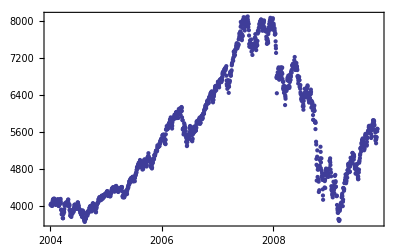

```mathematica
DateListPlot[FinancialData["DAX","Jan. 1, 2004"]]
```

#### Excercises

Plot a Logarithmic spirals of the form r=a ⅇ^(b θ)

Plot a four-leaved rose, r=cos^2 θ-sin^2 θ

Plot a cardoid r = 1 + sinθ

Plot a limaçon, r=1/2+ cosθ

### Labeling your plots

Required Reading:

Annotating & Combining Graphics

Especially when plotting multiple functions or datasets in a single graph it is important to clearly label each function or data set. One way to do so is to use text labels in the plot. We can use the Epilog option to do so:

```mathematica
Plot[{20Exp[.01 t], 12Exp[.03 t]},{t,0,40},
AxesOrigin->{0,0},
Epilog->{Text[Style["Factory A", FontSize->18],(* now the coordinates *){5,25}],
Text["Factory B",{5,10}]}
]
```

Alternatively you can use the function Tooltip to provide "mouseover" labels. These are labels that will appear only when the mouse is moved over a certain feature. Example:

```mathematica
Tooltip[x+y,"label"]
```

Our plot may be labels accordingly:

```mathematica
Plot[{
Tooltip[20Exp[.01 t],"Factory A"],
Tooltip[12Exp[.03 t],"Factory B"]},
{t,0,40},
AxesOrigin->{0,0}
] (* move the mouse over the curves *)
```

This is especially nice for ListPlot. You can use it to distinguish between datasets:

```mathematica
ListPlot[{Tooltip[(3/2)^Range[15],TraditionalForm[(3/2)^k]],Tooltip[Fibonacci[Range[15]],TraditionalForm[Fibonacci[k]]]},PlotStyle->PointSize[Medium]]
```

Or you can use Tooltip to indicate the value of individual datapoints:

```mathematica
ListPlot[Table[Tooltip[Prime[i]],{i,10}]]
```

### Plots with Legend

```mathematica
Needs["PlotLegends`"]
```

Required Reading

Plot Legends Package

To include plot legends, you need to load an additional package. But even then, the Mathematica's legend capabilities are lacking.

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2 π,2 π},PlotLegend->{"Sine","Cosine"}]
```

We can change thy style somewhat:

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2 π,2 π},PlotLegend->{"Sine","Cosine"},LegendShadow->None, LegendSize->0.5,LegendPosition->{1.2,0}]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,-2 π,2 π},PlotStyle->{Directive[Purple,Thick],Directive[Thick,Orange,Dashing[{.03}]]},PlotLegend->{"sin","cos"},LegendPosition->{.5,-.8},LegendTextSpace->0.5,LegendLabel->Style["Trig Funcs",14],LegendLabelSpace->.5,LegendOrientation->Vertical,LegendBackground->LightPurple,LegendShadow->{.02,-.02},Background->LightOrange,LegendSize->{0.5,0.5}]
```

The second way of placing a legend in a graphic is to use ShowLegend. With ShowLegend you specify the graphic and legend as arguments.

```mathematica
ShowLegend[DensityPlot[Sin[x y],{x,0,π},{y,0,π}],{ColorData["LakeColors"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-0.4}}]
```

```mathematica
ShowLegend[Plot3D[Sin[x y],{x,0,π},{y,0,π},ColorFunction->"Rainbow"],{ColorData["Rainbow"][1-#1]&,10," 1","-1",LegendPosition->{1.1,-0.4}}]
```

#### Custom Legend 1

It is also possible to construct your own legends:

```mathematica
Clear[legendPlot]
legendPlot[xl_List,d_,args___]:=Plot[xl,d,Epilog->Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],#1}&,xl]]],Offset[{-2,-2},Scaled[{1,1}]],{Right,Top}],args]
```

```mathematica
legendPlot[{Sin[x],Cos[x],Sinc[x]},{x,0,10}]
```

#### Custom Legend 2

Another way to create custom legends is here

```mathematica
Clear[legend];
legend[list_,pos_]:=Inset[Panel[Grid[MapIndexed[{Graphics[{ColorData[1,First@#2],Thick,Line[{{0,0},{1,0}}]},AspectRatio->.1,ImageSize->20],#1}&,list]]],pos,{Left,Top}];
```

```mathematica
Plot[{Re[PrimeZetaP[t]],Im[PrimeZetaP[t]]},{t,0.01,1},Epilog->{legend[{Re[PrimeZetaP[t]],Im[PrimeZetaP[t]]},Scaled[{0.1,0.9}]]}]
```

### Saving and Printing Graphics

When you want to save a graphic or print it you can use varios approaches. Take an example plot:

```mathematica
ListPolarPlot[Table[Sqrt[n],{n,100}],ImageSize->100]
```

If you click on the graph a reddish selection border appears. The use File ⊳ Print Selection ... to print the graph or use  File ⊳ Save Selection As ... to export your image as EPS, JPG or any other available data format. You can also click on the right output brackets to select the output cell and either use the right mouse click to save/print or use the menu items as above.

To be honest, Mathematica's printing and exporting capabilities is still somewhat lacking. Sometimes it might be necessary to save your graphics as PDF and then print it from acrobat viewer to get a nice printout. Wolfram aknowledges this deficit and promised improvements in the next releases.

### Excercises

#### Customize your Plots

Reproduce the following graph from  Cool Infographics

#### Customize your Plots II

Reproduce the following Business Week plot as good as possible:

The data points are: {2.9,2.45,2.5,3.5,3.7,3.0,1.75,0.75,0.3,0.2,1.9,1.6,0.5,-0.5,-2.8}

#### 4D data visualization

Consider possibilities to plot a 4-dim dataset. Use the following data:

```mathematica
(rad:=2Random[]-1;
data=Table[{xvar=rad,yvar=rad,zvar=rad,Abs[xvar yvar zvar]},{100}];)
```

#### Fourier-sine approximation to square wave

A square wave with unit amplitude and period 2π is defined by f[x+m π]=f[x] for any integer m and f[x]=Sign[x] for |x|<π.  This square wave can be approximated by a Fourier-sine series of the form

(f̃)_n[x]= 4/π  ∑_(k=1)^n Sin[(2k-1)x]/(2k-1)

where n is the order of approximation.  Produce a 2×3 graphics array which compares the first 6 approximations with the square-wave itself.

#### Antenna patterns

The angular distribution  of intensity produced by an array of n identical equally-spaced antennas which broadcast in phase at wave length λ has the form
f[n,d,λ,θ]=Sin[n π d/λ Sin[θ]]^2/Sin[π d/λ Sin[θ]]^2
where d is the spacing and θ the polar angle.  Use PolarPlot to display antenna patterns for n=4 and d/λ={1,4}.

#### Hydrogenic wave functions

Wave functions for the hydrogen atom take the form
ψ_(n,ℓ, m)(r,θ,ϕ)∝ⅇ^(-κ r) (κ r)^ℓ L_(n-ℓ-1)^(2 ℓ+1)(2 κ r) Y_ℓ^m(θ,ϕ)
where n is the principal (radial) quantum number, ℓ is the orbital angular momentum in units of ℏ, m is the magnetic (azimuthal) quantum number, and ℏ κ=√(2 μ E_b)is the wave number for positive binding energy E_b.  The radial dependence involves generalized Laguerre functions and the angular dependence spherical harmonics.  Note that we are not interested in the normalization of these functions at this time.  The probability density is given by the absolute square of the wave function, namely (|ψ|)^2.  Write a function that plots the probability density in the xy plane (θ=π/2) given values of the quantum numbers nℓm using Plot3D.   You will need to express the Cartesian coordinates in terms of spherical coordinates.  Write a similar function that uses DensityPlot.  Show several cases of each.

#### Sampling points

Write a function which displays the points sampled by Mathematica 's adaptive algorithm for Plot as vertical bars between the x-axis and the points themselves.

#### Potential and field for uniform sphere

The electric field of a uniformly charged sphere or the gravitational field of a sphere of uniform density both have the same shape.  Let ϕ=3/2-r^2/2 for r≤1 or ϕ=r^-1 for r≥1 represent the normalized potential, where r=√(x^2+y^2+z^2) is the distance from the center in units of the radius of the sphere.  The field if then f⃗=-OverVector[∇]ϕ.
a) Use ContourPlot to display equipotential lines in the xy plane (two-dimensions).
b) Use VectorPlot to display the force field in the xy plane.  Combine this plot with the equipotentials from the preceding exercise.
c) Use ContourPlot3D and VectorPlot3D to display equipotential surfaces and the vector field within a representative volume of space.